Assume we’re stabilizing vx(t) = vx0, and that there is an additional detuning Δ which is unknown but which is much smaller than 1/T2. Before breakdown, the evolution is (see previous notebook for derivation):

```mathematica
vyp[vx0_,t_,T2_]=(1-E^-(t/T2))*Δ*vx0*T2; (* Eq 15 in text*)
```

We’ve made the approximation that vx is constant before breakdown (i.e., is unaffected by detuning), which is true when Δ is small.

After   the  breakdown at time t0, there is free decay. In the  limit  of  small  detuning, we  have  (defining  tp = t - t0 and taking the first-order expansion in ΔT2):

```mathematica
vy[vx0_,tp_,tb_,T2_]=(vyp[vx0,t0,T2]+vx0*Δ*tp)*E^-(tp/T2); (*Eq 19 in text*)
```

In general the SNR goes like vy * N^(1/2), where N is the number of shots. In a given total time T to run the experiment, N = T / (t + ti), where t is the total evolution time and ti is the sum of all inactive times (for things like state preparation, measurement, reset, etc.). If ti >> T2, then N is constant for all protocols. In this case maximizing vy(t) over all time and initial state, like we did before, is optimal. On the other hand, if inactive time is negligible, then we instead optimize vy(t) / t^(1/2)  , the SNR per root total evolution time, per unit detuning:

```mathematica
SNR[vx0_,tp_,t0_,T2_] = (vy[vx0,tp,t0,T2]/Δ)/Sqrt[tp+t0] (*Eq 19 divided by sqrt(t), with the Δ dependence divided off*)
```

(ⅇ^(-tp/T2) ((1-ⅇ^(-t0/T2)) T2 vx0 Δ+tp vx0 Δ))/(√(t0+tp) Δ)

First let’s maximize this, leaving the breakdown t0 as a variable. The maximization happens at a time after the breakdown:

```mathematica
tpmax=tp/.Solve[D[SNR[vx0,tp,t0,T2],tp]==0,tp][[2]]
```

1/4 (-2 t0-T2+2 ⅇ^(-t0/T2) T2+ⅇ^(-t0/T2) √(8 ⅇ^(t0/T2) T2 (2 t0+T2-ⅇ^(t0/T2) T2)+(2 ⅇ^(t0/T2) t0-2 T2+ⅇ^(t0/T2) T2)^2))

We can clean that up a little bit

```mathematica
FullSimplify[tpmax,Assumptions->t0>0&&T2>0](*The solution is Eq 26*)
```

1/4 ⅇ^(-t0/T2) (2 T2-ⅇ^(t0/T2) (2 t0+T2)+√(4 T2^2+4 ⅇ^(t0/T2) T2 (2 t0+T2)+ⅇ^((2 t0)/T2) (4 t0^2+4 t0 T2-7 T2^2)))

Using this time  gives  a maximum  SNR per root evolution time, per unit detuning, of:

```mathematica
SNRmax[vx0_,t0_,T2_]=SNR[vx0,tpmax,t0,T2]
```

(ⅇ^(-(-2 t0-T2+2 ⅇ^(-t0/T2) T2+ⅇ^(-t0/T2) √(8 ⅇ^(t0/T2) T2 (2 t0+T2-ⅇ^(t0/T2) T2)+(2 ⅇ^(t0/T2) t0-2 T2+ⅇ^(t0/T2) T2)^2))/(4 T2)) ((1-ⅇ^(-t0/T2)) T2 vx0 Δ+1/4 (-2 t0-T2+2 ⅇ^(-t0/T2) T2+ⅇ^(-t0/T2) √(8 ⅇ^(t0/T2) T2 (2 t0+T2-ⅇ^(t0/T2) T2)+(2 ⅇ^(t0/T2) t0-2 T2+ⅇ^(t0/T2) T2)^2)) vx0 Δ))/(√(t0+1/4 (-2 t0-T2+2 ⅇ^(-t0/T2) T2+ⅇ^(-t0/T2) √(8 ⅇ^(t0/T2) T2 (2 t0+T2-ⅇ^(t0/T2) T2)+(2 ⅇ^(t0/T2) t0-2 T2+ⅇ^(t0/T2) T2)^2))) Δ)

We  can  simplify this a bit, but it’s still long:

```mathematica
FullSimplify[%,Assumptions->t0>0&&T2>0]
```

(ⅇ^((ⅇ^(-t0/T2) ((-2+ⅇ^(t0/T2)) T2-√(4 T2^2+4 ⅇ^(t0/T2) T2 (2 t0+T2)+ⅇ^((2 t0)/T2) (4 t0^2+4 t0 T2-7 T2^2))))/(4 T2)) (-2 T2+ⅇ^(t0/T2) (-2 t0+3 T2)+√(4 T2^2+4 ⅇ^(t0/T2) T2 (2 t0+T2)+ⅇ^((2 t0)/T2) (4 t0^2+4 t0 T2-7 T2^2))) vx0)/(2 √(ⅇ^(t0/T2) (2 t0-T2)+2 T2+√(4 T2^2+4 ⅇ^(t0/T2) T2 (2 t0+T2)+ⅇ^((2 t0)/T2) (4 t0^2+4 t0 T2-7 T2^2))))

There’s an exact expression for the breakdown time, here shown when vz(0)>0, vy(0)=0, and temperature = 0.

```mathematica
a[vx0_,T1_,T2_] = Sqrt[vx0^2/(T2/(4*T1))-1]; (*Eq 25*)
vz0[vx0_]=Sqrt[1-vx0^2];
tb[vx0_,T1_,T2_] = T1/a[vx0,T1,T2]*(ArcTan[1/a[vx0,T1,T2]]+ArcTan[(2*vz0[vx0]-1)/a[vx0,T1,T2]])+T1/2*Log[((2*vz0[vx0]-1)^2+a[vx0,T1,T2]^2)/(1+a[vx0,T1,T2]^2)];(*Eq 24*)
```

Now  we  need  to  replace t0->tb, which depends on T1, T2, and vx0. Then we need to maximize over vx0. It’s not possible to maximize analytically, but the graph shows it’s relatively well-behaved; here’s an example with T1 = T2 = 1:

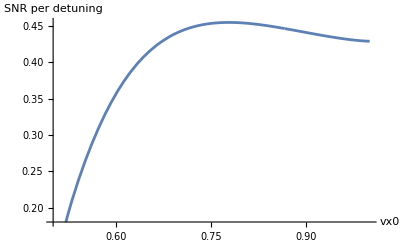

```mathematica
Plot[SNRmax[vx0,tb[vx0,1,1],1],{vx0,0.5,1}, AxesLabel->{"vx0","SNR per detuning"}]
```

We  can  also define the ratio to the SNR (per root time ) for Ramsey at a given detuning. First we need to take care of the case where breakdown doesn’t happen. In that case vy grows as vyp above, so it’s easy to optimize. Mathematica needs a little bit of help getting there though

```mathematica
D[vyp[vx0,t,T2]/Sqrt[t],t]
```

(ⅇ^(-t/T2) vx0 Δ)/(√t)-((1-ⅇ^(-t/T2)) T2 vx0 Δ)/(2 t^(3/2))

Multiply through a factor of sqrt(t) and divide of vx0 and then it solves just fine:

```mathematica
tnbmax[T2_] = t/.Solve[t*E^-(t/T2) - (1-E^-(t/T2))*T2/2==0,t][[2]] (*Eq 16*)
```

1/2 (-T2-2 T2 ProductLog[-1,-1/(2 √ⅇ)])

Now we can check if the optimum happens before breakdown, and if not, when we should measure and what the SNR ratio (stabilized to Ramsey) will be:

```mathematica
optBeforeBreak[vx0_,T1_,T2_]=If[vx0>1/2*Sqrt[T2/T1]&&tnbmax[T2]>Re[tb[vx0,T1,T2]] ,0,1];
tpmaxtemp[vx0_,T1_,T2_] = tpmax/.t0->tb[vx0,T1,1];
tmeas[vx0_,T1_,T2_]=If[optBeforeBreak[vx0,T1,T2]<0.5,tb[vx0,T1,T2]+tpmaxtemp[vx0,T1,T2],tnbmax[T2]];Rs[vx0_,T1_,T2_]=If[optBeforeBreak[vx0,T1,T2]<0.5,SNRmax[vx0,tb[vx0,T1,T2],T2]/(1/(√(2 ⅇ))),vyp[vx0,tnbmax[1],1]/Δ/Sqrt[tnbmax[1]]/(1/(√(2 ⅇ)))]
```

If[If[vx0>(√(T2/T1))/2&&1/2 (-T2-2 T2 ProductLog[-1,-1/(2 √ⅇ)])>Re[(T1 (ArcTan[1/(√(-1+(4 T1 vx0^2)/T2))]+ArcTan[(-1+2 √(1-vx0^2))/(√(-1+(4 T1 vx0^2)/T2))]))/(√(-1+(4 T1 vx0^2)/T2))+1/2 T1 Log[(T2 (-1+(4 T1 vx0^2)/T2+(-1+2 √(1-vx0^2))^2))/(4 T1 vx0^2)]],0,1]<0.5,SNRmax[vx0,tb[vx0,T1,T2],T2]/(1/(√(2 ⅇ))),vyp[vx0,tnbmax[1],1]/((Δ √tnbmax[1])/(√(2 ⅇ)))]

Here let’s plot it with a few different T1/T2 ratios:

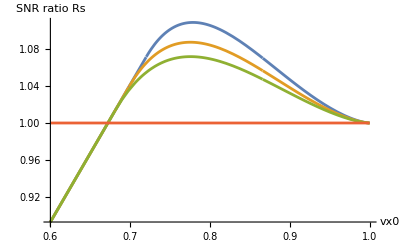

```mathematica
Plot[{Rs[vx0,0.7,1],Rs[vx0,0.8,1],Rs[vx0,0.9,1],1},{vx0,0.6,1},AxesLabel->{"vx0", "SNR ratio Rs"},PlotRange->All]
```

It goes above 1, indicating an advantage. We can be more precise and maximize numerically:

```mathematica
NMaximize[{Rs[vx0,1,1],vx0>0.7&&vx0<1},vx0]
```

{1.06017,{vx0→0.77759}}

We  see that when T1 = T2 and experiment idle time is negligible, there is an SNR improvement by a factor of 1.06 using an initial state vx0 = 0.77759.

What about the case T1 = 0.8 T2, which is roughly our experimental value?

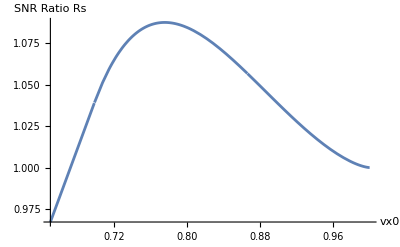

```mathematica
Plot[Rs[vx0,0.8,1],{vx0,0.65,1},PlotRange->All,AxesLabel->{"vx0","SNR Ratio Rs"}]
```

```mathematica
NMaximize[{Rs[vx0,0.8,1],vx0>0.7&&vx0<1},vx0]
```

{1.08744,{vx0→0.775383}}

So we have an improvement ratio 1.08744 closely matching the experimentally measured value. This occurs when the initial state vx0 = 0.775383, i.e. the initial state angle is θ = 0.282433π.
We’ll generate a dataset to use for plotting in the paper:

```mathematica
xypairs= Table[{ArcSin[vx0]/Pi,Rs[vx0,0.8,1]},{vx0,0.6,1,0.001}];
```

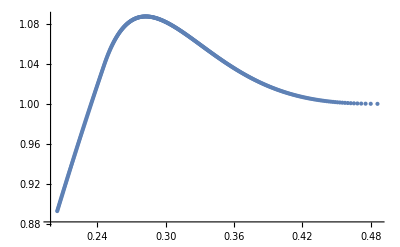

```mathematica
ListPlot[xypairs,PlotRange->All,PlotHighlighting->None]
```

We  can  now extend  this  optimization  over  all  T1/T2  ratios . Setting  T2 = 1  and  varying  T1, we  find :

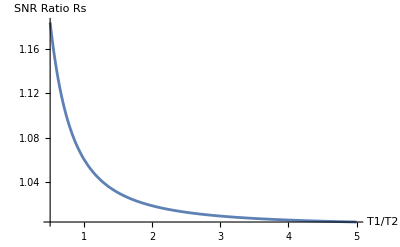

```mathematica
Plot[NMaximize[{Rs[vx0,T1,1],vx0>1/(2Sqrt[T1])&&vx0<1},vx0][[1]],{T1,0.5,5},PlotRange->All,AxesLabel->{"T1/T2","SNR Ratio Rs"}] (*Fig 3b bottom right*)
```

This again reaches a maximum when T1 = T2/2, with a value of 1.18418:

```mathematica
NMaximize[{Rs[vx0,0.5,1],vx0>1/(2Sqrt[0.5])&&vx0<1},vx0]
```

{1.18418,{vx0→0.8076}}

```mathematica
maxes = Table[NMaximize[{Rs[vx0,T1,1],vx0>1/(2Sqrt[T1])&&vx0<1},vx0][[1]],{T1,0.5,15,0.1}];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
states = Table[vx0/.NMaximize[{Rs[vx0,T1,1],vx0>1/(2Sqrt[T1])&&vx0<1},vx0][[2]],{T1,0.5,15,0.1}];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

The  orange curve below is the SNR improvement ratio, the blue is the initial state vx0 that produces that ratio.

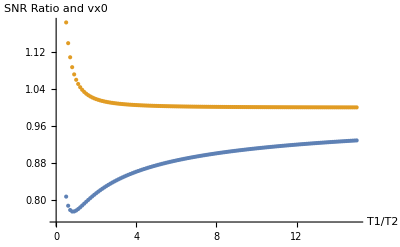

```mathematica
ListPlot[{states,maxes},DataRange->{0.5,15},AxesLabel->{"T1/T2","SNR Ratio and vx0"}]
```

The total evolution time before the measurement (in units of T2) is:

```mathematica
tpmaxtemp[Sin[Pi*0.27],0.75,1]+tb[Sin[Pi*0.27],0.75,1]
```

0.923921

Everything below this point is just generating datasets for experimental use

```mathematica
tmaxthetas = Table[{theta,optBeforeBreak[Sin[Pi*theta],0.75,1]*tnbmax[1]+(1-optBeforeBreak[Sin[Pi*theta],0.75,1])*(tpmaxtemp[Sin[Pi*theta],0.75,1]+tb[Sin[Pi*theta],0.75,1])},{theta,0.01,0.49,0.48/32}];
```

```mathematica
Re[tmaxthetas]//TableForm
```

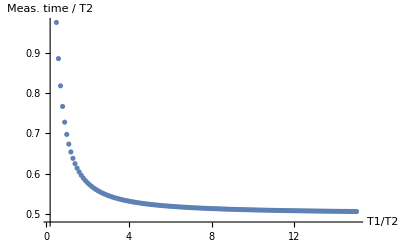

```mathematica
tptotmaxes = Table[(tpmaxtemp[vx0,T1,T2] + tb[vx0,T1,T2])/.{T1->(0.5+0.1*j),vx0->Part[states,j+1],T2->1},{j,0,Length[states]-1}];
ListPlot[tptotmaxes,DataRange->{0.5,15},AxesLabel->{"T1/T2","Meas. time / T2"},PlotRange->All]
```

```mathematica
maxesExpt = Table[{T1,NMaximize[{Rs[vx0,T1,1],vx0>1/(2Sqrt[T1])&&vx0<1},vx0][[1]]},{T1,0.5,5,0.1}];
```

```mathematica
maxesExpt//TableForm;
```

```mathematica
Rsexpt = Table[Rs[Sin[Pi*theta],T1,1],{theta,0.005,0.495,0.005},{T1,0.5,10,0.1}];
```

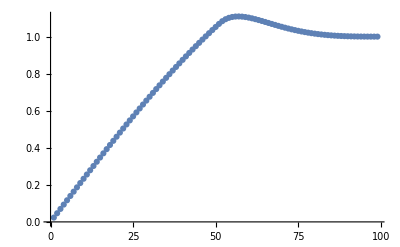

```mathematica
ListPlot[Rsexpt[[All,3]]]
```

It' s also nice to see how long after breakdown we should measure:

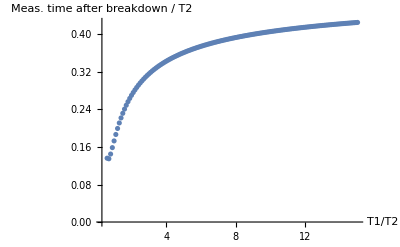

```mathematica
tpmaxtemp[vx0_,T1_,T2_] = tpmax/.t0->tb[vx0,T1,1];
tpmaxes = Table[tpmaxtemp[states[[j]],0.5+14.5/(Length[states]-1)*j,1],{j,0,Length[states]-1}];
ListPlot[tpmaxes, DataRange->{0.5,15},AxesLabel->{"T1/T2","Meas. time after breakdown / T2"},PlotRange->All]
```

So there’s definitely an opportunity to improve things with optimal control, since relaxation will populate the ground state during this time after breakdown.

To  optimize the protocol for any inactive time ti, we perform the same procedure as above, but we numerically optimize vy(t) / (t+ti)^1/2 instead of setting ti = 0 as we did above.
All the above analysis assumes measurement post-breakdown, but for some of the states simulated there isn’t a breakdown at all. The code below handles that case, using the larger of the pre-breakdown optimum and the post-breakdown optimum derived above.

First we solve for the optimal time pre-breakdown. Take the derivative of the SNR:

Make  some data for use in plotting in the paper:

```mathematica
xypairs= Table[{theta,Rs[Sin[Pi*theta],0.75,1]},{theta,0.005,0.495,0.005}];(*Table[{ArcSin[vx0]/Pi,Max[(Abs[{(1-UnitStep[Im[tb[vx0,0.75,1]]-0.001])*SNRmax[vx0,tb[vx0,0.75,1],1],(1-UnitStep[tnbmax-Re[tb[vx0,0.75,1]]]+UnitStep[Im[tb[vx0,0.75,1]]-0.001])*vyp[vx0,tnbmax,1]/d/Sqrt[tnbmax]}])/(1/Sqrt[2*E])]},{vx0,0.001,0.999,0.001}];*)
```

```mathematica
xypairs//TableForm
```

Also  define when we should do the measurement (i.e., when signal is max) as a function of initial state

```mathematica
tmeas[vx0_,T1_,T2_]=If[vx0>1/2*Sqrt[T2/T1],tb[vx0,T1,T2]+tpmaxtemp[vx0,T1,T2],tnbmax[T2]]
```

If[vx0>(√(T2/T1))/2,tb[vx0,T1,T2]+tpmaxtemp[vx0,T1,T2],tnbmax[T2]]

```mathematica
N[tmeas[0.3,0.75,1]]
```

1.25643

```mathematica
tmeaspears = Table[{theta,N[tmeas[Sin[Pi*theta],0.75,1]]},{theta,0.01,0.49,0.5/32}];
```

```mathematica
tmeas[Sin[Pi*0.283],0.75,1]
```

0.790602

```mathematica
tmeaspears//TableForm
```

Finally  let’s find the SNR ratio as a function of initial state and T1/T2, like we did with vy:

```mathematica
Rvpairs = Table[Rs[Sin[Pi*theta],T1,1],{theta,0.005,0.495,0.005},{T1,0.5,10,0.1}];
```

```mathematica
TableForm[Rvpairs];
```

```mathematica
thetamaxes = Table[{T1,theta/.NMaximize[{Rs[Sin[Pi*theta],T1,1],theta<0.5,theta>0},theta ][[2]]},{T1,0.5,5,0.01}];
```

```mathematica
thetamaxes//TableForm;
```

```mathematica
Sin[Pi*0.68]
```

0.844328

```mathematica
Rs[Sin[Pi*(0.5-0.188)],2.5,1]
```

1.0125

```mathematica
tmeasmaxes = Table[{N[tmeas[Sin[Pi*thetamaxes[[ii,2]]],thetamaxes[[ii,1]],1]]},{ii,1,451}];
```

```mathematica
tmeasmaxes//TableForm
```

```mathematica
Rs[Sin[0.373*Pi],0.82,1]
```

1.02612

```mathematica
NMaximize[Rs[Sin[Pi*theta],0.764,1],{theta,0.1,0.4}]
```

{1.09435,{theta→0.282782}}

```mathematica
Sin[Pi*0.282782]
```

0.776055